```mathematica
Clear["Global`*"]
```

```mathematica
(*Below are a bunch of built-in functions. Most are only needed for the "Constrained" and "UnConstrained" functions.*)

(*RowDelete takes a matrix and deletes the specified rows*)
RowDelete[x_,entries_]:=Module[{list},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]

(*ColumnDelete will take a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]

(*AddZeroToRow will, you guessed it, add a zero to a row vector! Wherever you want it!*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]

(*AddZerosToRow will add any number of zeros to a row vector in any places you want.*)
AddZerosToRow[x_,entries_]:=Module[{y,list},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]

(*Ok, Here is the main point! UnConstrained will take a dataset (imported from a csv file or similar) and produce a matrix "D" that incorporates least squares estimates for the "A" vector and "B" community matrix.*)
UnConstrained[data_]:=Module[{X,Y,Z,D,d0,p,one,c},
p=Length[data[[1]]];
X=data[[1;;Length[data]-1]];
Y=data[[2;;Length[data]]];
one={Table[1,{i,1,Length[data]-1}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
d0={Y[[All,k]]}.Z.Inverse[Transpose[Z].Z];
D=Join[D,d0]
];
D
]

(*Here is the other main point! Constrained will take a dataset AND a list of B matrix entries and produce a matrix "D" that incorporates the CONSTRAINED least squares estimates for the "A" vector and "B" community matrix. The constraints must be entered as a list of pairs. For example: if we enter {{1,2},{3,1}}, then the B matrix will have zeros in these positions. *)
Constrained[data_,constraints_]:=Module[{X,Y,Z,D,d0,p,one,c},
p=Length[data[[1]]];
X=data[[1;;Length[data]-1]];
Y=data[[2;;Length[data]]];
one={Table[1,{i,1,Length[data]-1}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D
]
```

```mathematica
(*This is the code to import data select range and log transform. You can see that I have edited the data set so it only contains the stuff I want. I have also set the range so that I avoid all zeros. You can play with the range to see what this does to the estimates derived from the dataset. You will also have to make sure your directory is set correctly so Mathematica can actually find the file you specify.*)

SetDirectory["C:\\Users\\Jackson\\Dropbox\\Weak interactions"];
rawdata=Import["Dap_edit.csv"];
data=Log[rawdata[[10;;Length[rawdata]]]];
p=Length[data[[1]]];
```

(3.82402 | -0.00511042 | 0.154767 | -0.578987
-1.33051 | 0.230167 | -0.286551 | -0.10915
-2.84845 | 0.384021 | -0.651591 | 0.429339)

(2.75619 | 0.430047 | -0.434082 | 0
-1.33051 | 0.230167 | -0.286551 | -0.10915
-1.43116 | 0 | -0.252979 | 0.173091)

{0.221832,0.102523,0.102523}

{0.280589,0.280589,0.202096}

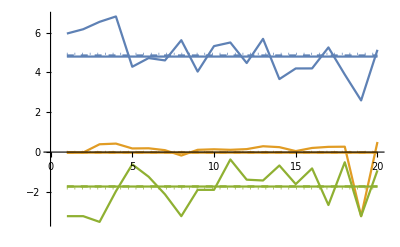

```mathematica
(*Compute various estimates of MAR model parameters, eigenvalues, and make some graphs.*)

(*Show the estimated matrices in a nice form. For this particular example what comes out is a 3 by 4 matrix. The first column is the "A" vector and the remaining 3 by 3 matrix is the "B" community matrix. For the constrained estimate I have chosed to make the {1,3} and {3,1} entries zero. I.e. I am forcing the assumption of no direct effect between daphinia and inedible algae.*)
MatrixForm[UnConstrained[data]]
MatrixForm[Constrained[data,{{1,3},{3,1}}]]

(*Here I am just naming the vectors and matrices in order to compute eigenvalues and make plots. None of this produces an output (since there is a semicolon at the end of each line).*)
AUnCon=UnConstrained[data][[All,1]];
ACon=Constrained[data,{{1,3},{3,1}}][[All,1]];
BUnCon=UnConstrained[data][[All,2;;p+1]];
BCon=Constrained[data,{{1,3},{3,1}}][[All,2;;p+1]];
MeanUnCon=Inverse[IdentityMatrix[p]-BUnCon].AUnCon;
MeanCon=Inverse[IdentityMatrix[p]-BCon].ACon;

(*Fins the eigenvalues of the B matrices. The absolute value is so that if there are complex eigenvalues these will be shown as the distance from the origin.*)
Abs[Eigenvalues[BUnCon]]
Abs[Eigenvalues[BCon]]

(*This makes a plot of the data itself. The vaious horizontal lines are means: solid=means of unconstrained stationary dist; dashed=means of constrained stationary dist; dotted=means of actual dataset.*)
Show[ListLinePlot[Transpose[data]],ListLinePlot[Transpose[Table[MeanUnCon,{i,1,Length[data]}]]],ListLinePlot[Transpose[Table[MeanCon,{i,1,Length[data]}]],PlotStyle->Dashed],
ListLinePlot[Transpose[Table[Mean[data],{i,1,Length[data]}]],PlotStyle->Dotted]]
```

```mathematica
({{4.484392604035449, 0.22500843279828087, -0.455504617800468, 0.2686202160823834}, {0.7865717275529933, -0.1400649620504294, 0.8523951858414425, -0.044102155197608406}, {-1.3453690708161083, -0.12125963192367789, 0.9295254405387476, 0.07003267839937255}})
```

{{4.48439,0.225008,-0.455505,0.26862},{0.786572,-0.140065,0.852395,-0.0441022},{-1.34537,-0.12126,0.929525,0.0700327}}